```mathematica
(* Joe Hesse-Withbroe Senior Thesis: 
Implementing flying disc equation of motion into mathematica.
This code is a single-solver i.e. it'll solve the equation of motion for ONE set of initial conditions.
It is a good place to trial any changes to the different forces to sanity-check the resulss.
It is not a good place to run a large number of simulations -- use Functional_solver.m instead.
It will visualize a variety of useful things -- accelerations in the various directions that are the result of the different forces, allowing you to compare the relative magnitudes of the different effecss.
It will also animate the simulated trajectory & orientation of the disc over the course of flight, again good for a sanity-check on any new additions/changes to the original equations of motion. *)
```

```mathematica
(*  Constants definition - ruellia seeds *)
(*g = 9.81; (* Acceleration due to gravity *)
ρ = 1.225; (* Density of air *)
R = .00125; (* 2.5 mm diameter *)
d = .00025; (* Thickness ~ estimated. Max thickness ~.45mm at center, tapers down to ~.01mm at ends*)
m = .0000017;  (* ~2 mg *)
ω = 1000*2π; (* Rotation rate in rad/s *)
μ=.000018; (*dynamic viscosity of air -- not currently used*)
e=.5; (* induced drag efficiency -- ellipitcal wing = 1, rectangular = 0.7 -- choose intermediate *)
L = 1/2 m*R^2*ω; (* ang mom. thin disc rotating about axis of symmetry *)*)

(*Coaster*)
g = 9.81; (* Acceleration due to gravity *)
ρ = 1.225; (* Density of air *)
R = .053; (* 5 cm radius coaster *)
d = .0017; (* Thickness ~ estimated. *)
m = .0059;  (* 5.9 g *)
ω = 7.9*2π; (* Rotation rate in rad/s *)
μ=.000018; (*dynamic viscosity of air -- not currently used*)
e=.5; (* induced drag efficiency -- ellipitcal wing = 1, rectangular = 0.7 -- choose intermediate -- not currently used (using experimental drag coefficient instead) *)
L = 1/2 m*R^2*ω; (* ang mom. thin disc rotating about axis of symmetry *) 

Subscript[α, crit]= (40)*(2π)/360;
Subscript[α, decay] = 0.1;
```

```mathematica
(* Component-wise force definitions. Constant terms in front give magnitude, jumbled messes are the direction -- look really bad because of the need to convert between body & lab frame*)

V[t] = √(x'[t]^2+y'[t]^2+z'[t]^2); (* Velocity magnitude *)

(* Angular momentum components in lab frame *)
Lx[t]=L*(x'[t]/V[t] Sin[α[t]]+y'[t]/V[t] Cos[α[t]]Cos[ϕ[t]]+z'[t]/V[t] Cos[α[t]]Sin[ϕ[t]]);
Ly[t]=L*(y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);
Lz[t]=L*(z'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-x'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]);

(*Lift components in lab frame - defined using the above ang mom components*)
(* Lift as function of v and l components*)
FLx[t]=(((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (Ly[t] x'[t] y'[t]+Lz[t] x'[t] z'[t]-Lx[t] (y'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2)))));
FLy[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (-y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t] (x'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));
FLz[t]=-((π^2 R^2 ρ)/2 Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]))(Lz[t] (x'[t]^2+y'[t]^2)-(Lx[t] x'[t]+Ly[t] y'[t]) z'[t]) (x'[t]^2+y'[t]^2+z'[t]^2))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (Lz[t]^2 (x'[t]^2+y'[t]^2)-2 Lx[t] Lz[t] x'[t] z'[t]-2 Ly[t] y'[t] (Lx[t] x'[t]+Lz[t] z'[t])+Ly[t]^2 (x'[t]^2+z'[t]^2)+Lx[t]^2 (y'[t]^2+z'[t]^2))));



(* Drag force components. Using the experimentally determined value of CD for Ruellia seeds *)
(* Experimental drag expression based on measured Cd for R ciliatiflora *)
Subscript[C, D] = 0.301; (*5% uncertainity interval: (.259, .343) *)
Dx[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*x'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dy[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*y'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));
Dz[t] = -(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*z'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]));

(* Experimental magnus exrpression based on measured Cm for R ciliatiflora *)
Subscript[C, M]=0.0351;(*5% uncertainity interval: (.018, .052) *)
Mx[t] = -1/2 Subscript[C, M] ρ(d*2R)V[t](y'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2)))-z'[t](y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]]));
My[t] = -1/2 Subscript[C, M] ρ(d*2R)V[t](z'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t])-x'[t](Sin[α[t]]*z'[t]/(√(x'[t]^2+z'[t]^2))-Cos[α[t]]Sin[ϕ[t]]*x'[t]/(√(x'[t]^2+z'[t]^2))));
Mz[t] =-1/2 Subscript[C, M] ρ(d*2R)V[t](x'[t](y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]])-y'[t](Sin[α[t]]*x'[t]/V[t]+Cos[α[t]]Cos[ϕ[t]]*y'[t]/V[t]+Cos[α[t]]Sin[ϕ[t]]*z'[t]/V[t]));
```

```mathematica
(* DE Definitions  *)
Subscript[eq, α] = α'[t] == (g *√(x'[t]^2+z'[t]^2))/V[t]^2 Cos[ϕ[t]]-(ρ*V[t]*π^2*R^2)/(2m)Sin[2α[t]](1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])));
Subscript[eq, ϕ] = ϕ'[t] == -(π^3*R^3 ρ*V[t]^2)/(16*L)Sin[2*α[t]](1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])));
Subscript[eq, x] = x''[t]==1/m(FLx[t]+Dx[t]+Mx[t]);
Subscript[eq, y] = y''[t]== 1/m(FLy[t]+Dy[t]+My[t])-g;
Subscript[eq, z] = z''[t] ==1/m(FLz[t]+Dz[t]+Mz[t]);
```

```mathematica
(* Initial Conds & Solver --- *)
Subscript[x, o]=0;
Subscript[y, o]=0.98; (* Initial launch height in m *)
Subscript[z, o]=0;
Subscript[α, o]=(0.1)*((2*π)/360); (* α could probably be exactly 0 but giving it a small value may help with numerical stability -- Since Lift is defined with respect to the L-V plane (plane defined by Ang mom and Velocity), if L and V become colinear, lift does not have a unique specification -- This only happens at certains pairs of ϕ and α where both are "clean" values (ie multiples of π/2 -- i think when alpha = +- 90 -- I think this is related to "gimbal locking"). In any of these dangerous orientations, the symmetry of the situation is such that lift would be 0 anyway but this is difficult to code into the equations, and physics prevents these bad orientatiosn from being reached in the middle of the sim. The only way these bad orientations can be reached is if the intiial conditions match one of the bad orientations. *)
Subscript[ϕ, o] = (0)*((2*π)/360); (* 270 degrees = bkspin, 90 = tpspin. 180=side-spin (forehand) 0=side-spin (backhand), May be reversed if ω is negative, but there should be no reason to do that - every initial launch orientation is achievable by varying α and ϕ only.*)
Subscript[vx, o]=2.6*Cos[1.9*((2*π)/360)];
Subscript[vy, o]=2.6*Sin[1.9*((2*π)/360)];
Subscript[vz, o]=0.0; 

soln = NDSolve[{
(* 5 ODES *)
 Subscript[eq, α],Subscript[eq, ϕ], Subscript[eq, x], Subscript[eq, y],Subscript[eq, z], 
(*Subscript[tempEq, α],Subscript[tempEq, ϕ], Subscript[eq, x], Subscript[eq, y],Subscript[eq, z],*)
(* Initial conditions *)
ϕ[0]==Subscript[ϕ, o],
α[0]==Subscript[α, o],
x[0]==Subscript[x, o],x'[0]==Subscript[vx, o],
y[0]==Subscript[y, o],y'[0]==Subscript[vy, o],
z[0]==Subscript[z, o],z'[0]==Subscript[vz, o]},

{α,ϕ,x,y,z},{t,0,10} (* Solve equations for t ranging from 0 to 10. Realistically only need a couple seconds, 10 gives a big safety buffer *)]
```

{{α→InterpolatingFunction[…],ϕ→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
xsol = x/. First[soln];
ysol = y/. First[soln];
zsol = z/. First[soln];
ϕsol = ϕ/. First[soln];
αsol = α/. First[soln];
temp = Table[{t,xsol[t], ysol[t], zsol[t], ϕsol[t], αsol[t]},{t,0,3,.01}];

Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\SimData\\CoasterTrajectory.csv",temp
];
```

0.752297

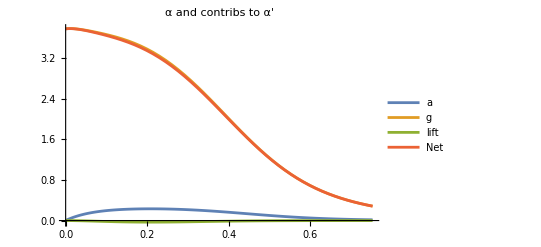

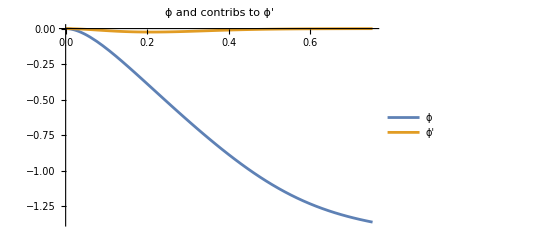

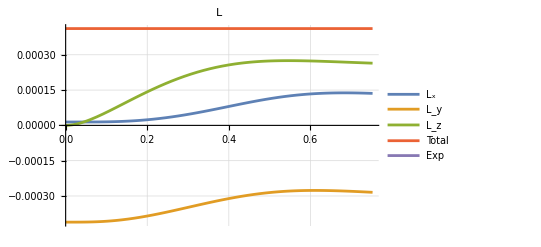

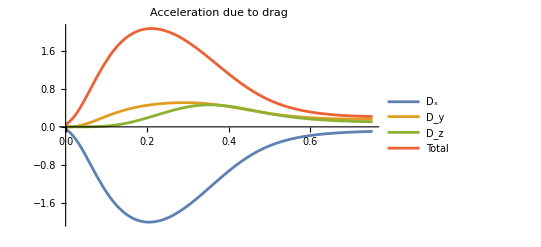

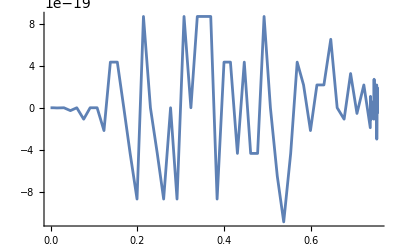

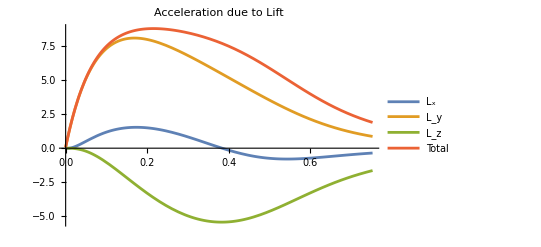

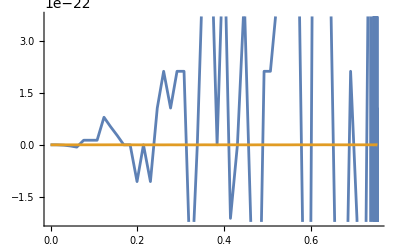

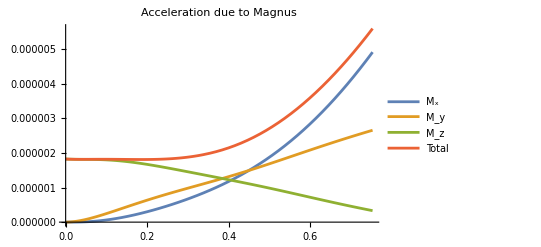

-Graphics3D-

```mathematica
Subscript[t, end] = 2.5;

(* get time disc hits ground - This part will error if the disc hasnt landed in the time specified in the findroot command. USually means that something is wrong w/ the equation, because a force is keeping the disc aloft far too long *)
tland = Part[FindRoot[0==y[t]/.soln,{t,.1, 10},MaxIterations->100000, Method->"Brent"],1] //Last
tland=tland;
L = 1/2 m*R^2*ω;

alphaeval=α[t]/.soln;
alphaGraveval=(g *√(x'[t]^2+z'[t]^2))/V[t]^2 Cos[ϕ[t]]/.soln;
alphaLifteval=-(ρ*V[t]*π^2*R^2)/(2m)Sin[2α[t]](1/(1+E^(Abs[α[t]-Subscript[α, crit]]/Subscript[α, decay])))/.soln;
phieval = ϕ[t]/.soln;
phiLifteval=-(π^3*R^3 ρ*V[t]^2)/(16*L)Sin[2*α[t]](1/(1+E^(Abs[α[t]-Subscript[α, crit]]/Subscript[α, decay])))/.soln;
Plot[{alphaeval,alphaGraveval,alphaLifteval,(alphaGraveval+alphaLifteval)},{t,0,tland},
PlotLegends->{"a","g","lift","Net"},
PlotLabel->"α and contribs to α'"
]

Plot[{phieval,phiLifteval},{t,0,tland},
PlotLegends->{"ϕ","ϕ'"},
PlotLabel->"ϕ and contribs to ϕ'"]

(* Extract the various accelerations due to forces experienced and plot them over time *)
(* Gives orientation of disc over time - magn should be constant*)
(* Angular momentum components in lab frame *)
angmomX=L*(x'[t]/(√(x'[t]^2+y'[t]^2+z'[t]^2))Sin[α[t]]+y'[t]/V[t] Cos[α[t]]Cos[ϕ[t]]+z'[t]/V[t] Cos[α[t]]Sin[ϕ[t]])/.soln;
angmomY=L*(y'[t]/V[t] x'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-(√(x'[t]^2+z'[t]^2))/V[t] Cos[α[t]]Cos[ϕ[t]]+y'[t]/V[t] z'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]])/.soln;
angmomZ=L*(z'[t]/(√(x'[t]^2+z'[t]^2))Sin[α[t]]-x'[t]/(√(x'[t]^2+z'[t]^2))Cos[α[t]]Sin[ϕ[t]])/.soln;
Plot[{angmomX,angmomY,angmomZ, √(angmomX^2+angmomY^2+angmomZ^2),L[t]},{t,0,tland*1},
PlotLegends->{"L_x","L_y","L_z", "Total", "Exp"},
PlotLabel->"L",
GridLines->Automatic]

Dxeval =-1/m (((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*x'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]))/.soln;
Dyeval = -1/m(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*y'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]))/.soln;
Dzeval = -1/m(((Subscript[C, D]+(π^2*Abs[Sin[α[t]]]^2)/e(1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])))^2)*ρ)/2 V[t]*z'[t](π*R^2 Abs[Sin[α[t]]]+2d*R*Abs[Cos[α[t]]]))/.soln;


plotDrag = Plot[{Dxeval,Dyeval,Dzeval, √(Dxeval^2+Dyeval^2+Dzeval^2)},{t,0,tland*1},
PlotLegends->{"D_x","D_y","D_z", "Total"},
PlotLabel->"Acceleration due to drag"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_drag.jpg",plotDrag];*)



(*Lift components in lab frame - defined using the above ang mom components*)
(* Lift as function of v and l components*)
FLxeval=(((π^2 R^2 ρ)/(2m)Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (angmomY x'[t] y'[t]+angmomZ x'[t] z'[t]-angmomX (y'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (angmomZ^2 (x'[t]^2+y'[t]^2)-2 angmomX angmomZ x'[t] z'[t]-2 angmomY y'[t] (angmomX x'[t]+angmomZ z'[t])+angmomY^2 (x'[t]^2+z'[t]^2)+angmomX^2 (y'[t]^2+z'[t]^2)))))/.soln;
FLyeval=-((π^2 R^2 ρ)/(2m)Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay])) (x'[t]^2+y'[t]^2+z'[t]^2) (-y'[t] (angmomX x'[t]+angmomZ z'[t])+angmomY (x'[t]^2+z'[t]^2)))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (angmomZ^2 (x'[t]^2+y'[t]^2)-2 angmomX angmomZ x'[t] z'[t]-2 angmomY y'[t] (angmomX x'[t]+angmomZ z'[t])+angmomY^2 (x'[t]^2+z'[t]^2)+angmomX^2 (y'[t]^2+z'[t]^2))))/.soln;
FLzeval=-((π^2 R^2 ρ)/(2m)Sin[2α[t]] 1/(1+E^((Abs[α[t]]-Subscript[α, crit])/Subscript[α, decay]))(angmomZ (x'[t]^2+y'[t]^2)-(angmomX x'[t]+angmomY y'[t]) z'[t]) (x'[t]^2+y'[t]^2+z'[t]^2))/(√((x'[t]^2+y'[t]^2+z'[t]^2) (angmomZ^2 (x'[t]^2+y'[t]^2)-2 angmomX angmomZ x'[t] z'[t]-2 angmomY y'[t] (angmomX x'[t]+angmomZ z'[t])+angmomY^2 (x'[t]^2+z'[t]^2)+angmomX^2 (y'[t]^2+z'[t]^2))))/.soln;

(*Ensure lift lies in plane of L and V*)
liftDirectionCheck = FLxeval*(y'[t]*angmomZ-z'[t]*angmomY)+FLyeval*(z'[t]angmomX-x'[t]angmomZ)+FLzeval*(x'[t]*angmomY-y'[t]*angmomX)/.soln;
Plot[liftDirectionCheck, {t,0,tland}]


plotLift = Plot[{FLxeval,FLyeval,FLzeval,√(FLxeval^2+FLyeval^2+FLzeval^2)},{t,0,tland},
PlotLegends->{"L_x","L_y","L_z", "Total"},
PlotLabel->"Acceleration due to Lift"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_lift.jpg",plotLift];*)


(* Magnus effect accelerations *)
Mxeval = -1/(2m)Subscript[C, M] ρ(d*2R)V[t](y'[t]angmomZ-z'[t]angmomY)/.soln;
Myeval = -1/(2m)Subscript[C, M] ρ(d*2R)V[t](z'[t]angmomX-x'[t]angmomZ)/.soln;
Mzeval = -1/(2m)Subscript[C, M] ρ(d*2R)V[t](x'[t]angmomY-y'[t]angmomX)/.soln;

magDirectionCheck1 = (Mxeval*(x'[t])+Myeval*(y'[t])+Mzeval*(z'[t]))/.soln;
magDirectionCheck2 = (Mxeval*(angmomX)+Myeval*(angmomY)+Mzeval*(angmomZ))/.soln;
Plot[{magDirectionCheck1,magDirectionCheck2}, {t,0,tland}]

plotMag = Plot[{Mxeval,Myeval,Mzeval,√(Mxeval^2+Myeval^2+Mzeval^2)},{t,0,tland},
PlotLegends->{"M_x","M_y","M_z", "Total"},
PlotLabel->"Acceleration due to Magnus"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_mag.jpg",plotMag];*)

(* Combined plots *)
plotNet = Plot[{√(Dxeval^2+Dyeval^2+Dzeval^2),
√(FLxeval^2+FLyeval^2+FLzeval^2),
√(Mxeval^2+Myeval^2+Mzeval^2)},{t,0,tland},
PlotLegends->{"Total Drag",
"Total Lift",
"Total Magnus"},
PlotStyle->{
{Brown},
{Purple},
{Red}},
PlotLabel->"Total Accelerations"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_net.jpg",plotNet];*)

plotX = Plot[{Dxeval,
FLxeval,
Mxeval,(Dxeval+FLxeval+Mxeval)},{t,0,tland},
PlotLegends->{"D_x",
"L_x",
"M_x",
"Net"},
PlotStyle->{
{Brown},
{Purple},
{Red},
{Black}},
PlotLabel->"Accelerations X"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_x.jpg",plotX];*)

plotY = Plot[{Dyeval,
FLyeval,
Myeval,
(Dyeval+FLyeval+Myeval)},{t,0,tland},
PlotLegends->{"D_y",
"L_y",
"M_y",
"Net"},
PlotStyle->{
{Brown},
{Purple},
{Red},
{Black}},
PlotLabel->"Accelerations Y"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_y.jpg",plotY];*)

plotZ = Plot[{Dzeval,
FLzeval,
Mzeval,
(Dzeval+FLzeval+Mzeval)},{t,0,tland},
PlotLegends->{"D_z",
"L_z",
"M_z",
"Net"},
PlotStyle->{
{Brown},
{Purple},
{Red},
{Black}},
PlotLabel->"Accelerations Z"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_z.jpg",plotZ];*)

(*Plot[{Dxeval,Dyeval,Dzeval,√(Dxeval^2+Dyeval^2+Dzeval^2),
FLxeval,FLyeval,FLzeval,√(FLxeval^2+FLyeval^2+FLzeval^2),
Mxeval,Myeval,Mzeval,√(Mxeval^2+Myeval^2+Mzeval^2)},{t,0,tland},
PlotLegends->{"D_x","D_y","D_z", "Total Drag",
"L_x","L_y","L_z", "Total Lift",
"M_x","M_y","M_z", "Total Magnus"},
PlotStyle->{
{Brown,Dashed},{Brown,Dotted},{Brown,DotDashed}, {Brown},
{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed}, {Purple},
{Red,Dashed},{Red,Dotted},{Red,DotDashed},{Red}},
PlotLabel->"Accelerations"]*)


plotAngle= Plot[{(α[t]/.soln)*360/(2π),(ϕ[t]/.soln)*360/(2π),(3π)/2*360/(2π),-π/2*360/(2π),π/2*360/(2π)},{t,0,tland},
PlotLabel->"Angles over flight",
PlotLegends->{"α","ϕ", "Stable","Stable","Unstable"},
PlotStyle->{{Blue},{Orange},{Green,Dashed},{Green,Dashed},{Red,Dashed}}]
Plot[(α[t]/.soln)*360/(2π), {t,0,tland},
PlotLabel->"Alpha over flight"]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_angles.jpg",plotAngle];*)

plotXY = ParametricPlot[{Evaluate[{x[t],y[t]}/.soln],{Subscript[vx, o]*t+Subscript[x, o],(-g*t^2)/2+Subscript[vy, o]*t+Subscript[y, o]}},{t,0,tland*1.1},
PlotRange->{{0,15},{0,15}}, 
PlotLabel->"Projected Trajectory XY Plane (vertical 'camera' plane) ",
PlotLegends->{"Disc","Vacuum"}]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_projxy.jpg",plotXY];*)

plotXZ = ParametricPlot[{Evaluate[{x[t],z[t]}/.soln],{Subscript[vx, o]*t+Subscript[x, o],Subscript[vz, o]*t+Subscript[z, o]}},{t,0,tland},
PlotRange->{{0,15},{-7.5,7.5}}, 
PlotLabel->"Projected Trajectory XZ Plane (Bird's eye view)",
PlotLegends->{"Disc","Vacuum"}]
(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_projxz.jpg",plotXZ];*)

 Plot[{y[t]/.soln,(-g*t^2)/2+Subscript[vy, o]*t+Subscript[y, o]},{t,0,tland},
PlotLabel->"Vertical Position (y-coord) vs time",
PlotLegends->{"Disc","Vacuum"}]
 Plot[{x[t]/.soln,(Subscript[vx, o])*t},{t,0,tland},
PlotLabel->"Horizontal Position (x-coord) vs time",
PlotLegends->{"Disc","Vacuum"}]

Plot[{z[t]/.soln,(Subscript[vz, o]*t)},{t,0,tland},
PlotLabel->"Off-horizontal position (z-coord) vs time",
PlotLegends->{"Disc","Vacuum"},
GridLines->Automatic]

Plot[{√(x[t]^2+z[t]^2)/.soln,√((Subscript[vx, o]*t)^2+(Subscript[vz, o]*t)^2)},{t,0,tland},
PlotLabel->"Net-horizontal displacement (x-z quadrature) vs time",
PlotLegends->{"Disc","Vacuum"}]


plotXYZ = ParametricPlot3D[{Evaluate[{x[t],y[t],z[t]}/.soln],{Subscript[vx, o]*t+Subscript[x, o],(-g*t^2)/2+Subscript[vy, o]*t+Subscript[y, o],Subscript[vz, o]*t+Subscript[z, o]}},{t,0,tland*1.1},
PlotRange->{{0,15},{0,4},{-5,5}}, 
PlotLabel->"3D trajectory ",
PlotLegends->{"Disc","Vacuum"},
FaceGrids->{{1,0,0},{0,-1,0},{0,0,-1}},
ViewAngle->Automatic,
ViewCenter->{0.5,0.5,0.5},
ViewMatrix->Automatic,
ViewPoint->{-2.742207823021334,1.6806221213300292,1.051572888893944},
ViewProjection->Automatic,
ViewRange->All,
ViewVector->Automatic,
ViewVertical->{-0.09658492883362392,0.9941483303666797,0.04837818466361288}]

(*Export["C:\\Users\\hesse\\Desktop\\F21\\Thesis\\figures\\Results\\simple\\\\\\seed\\topspin\\sd_ts_3D.jpg",plotXYZ];*)

(* Impulse due to selected forces *)
(*NIntegrate[Lx,{t,0,2}]
NIntegrate[Ly,{t,0,2}]
NIntegrate[g,{t,0,2}]
NIntegrate[Dx,{t,0,2}]*)
```

```mathematica
(* Animation block *)
(* Depending on choice of initial conditions, accelerations due to various forces may be quite small - so the scaled vectors may be tiny -can manually adjust scales below. 
TODO: implement adapative scaling that looks at the maximum value of each accelatation to guide scaling decisions... effort-reward ratio seems lacking for this *)

Subscript[α, sol][t_]=α[t]/.soln;
Subscript[ϕ, sol][t_]= ϕ[t]/.soln;
Subscript[x, sol][t_]= x[t]/.soln;
Subscript[y, sol][t_] = y[t]/.soln;
Subscript[z, sol][t_] = z[t]/.soln;

d=.125; (* thickness of disc object *)
l=2; (* scaling for L vector *)
rad=1; (* radius of disc (solely visual) *)
scaleLift = 1;(* scaling for lift vectors *)
scaleDrag = 12; (* scaling for drag vector *)
scaleMag = 500000000000; (* scaling for magnus vector *)
scaleL =200;  (* scaling for ang mom vec *)
scaleV = .4;
rng = 3; (* range of 3d graphics cube - i dont think this appears anywhere but i dont want to break anything *)
frameloc = 2; (* center of coordinate frame object *)

Animate[
Graphics3D[
{
(* disc object *)

Cylinder[{
{Part[Subscript[x, sol][t], 1]-d*(Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]+Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Cos[Part[Subscript[ϕ, sol][t], 1]]+Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]]),
Part[Subscript[y, sol][t], 1]-d*(Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]-Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Cos[Part[Subscript[ϕ, sol][t], 1]]+Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]]),
Part[Subscript[z, sol][t], 1]-d*(Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]-Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]])
},
{Part[Subscript[x, sol][t], 1]+d*(Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]+Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Cos[Part[Subscript[ϕ, sol][t], 1]]+Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]]),
Part[Subscript[y, sol][t], 1]+d*(Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]-Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Cos[Part[Subscript[ϕ, sol][t], 1]]+Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]]),
Part[Subscript[z, sol][t], 1]+d*(Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]-Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]])}
},
rad],

(* L VECTOR GRAPHIC *)

Black,Arrow[Tube[{{Part[Subscript[x, sol][t],1],Part[Subscript[y, sol][t],1],Part[Subscript[z, sol][t],1]},
{Part[Subscript[x, sol][t], 1]+l*(Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]+Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Cos[Part[Subscript[ϕ, sol][t], 1]]+Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]]),
Part[Subscript[y, sol][t], 1]+l*(Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]-Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Cos[Part[Subscript[ϕ, sol][t], 1]]+Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[y, sol]'[t], 1]]]Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]]),
Part[Subscript[z, sol][t], 1]+l*(Sin[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Sin[Part[Subscript[α, sol][t], 1]]-Cos[ArcTan[Part[Subscript[x, sol]'[t], 1],Part[Subscript[z, sol]'[t], 1]]]Cos[Part[Subscript[α, sol][t], 1]]Sin[Part[Subscript[ϕ, sol][t], 1]])}},
0.05]],


(* V VECTOR GRAPHIC *)

Orange,Arrow[Tube[{{Part[Subscript[x, sol][t],1],Part[Subscript[y, sol][t],1],Part[Subscript[z, sol][t],1]},
{Part[Subscript[x, sol][t],1]+scaleV*Part[Subscript[x, sol]'[t], 1],
Part[Subscript[y, sol][t],1]+scaleV*Part[Subscript[y, sol]'[t], 1],
Part[Subscript[z, sol][t],1]+scaleV*Part[Subscript[z, sol]'[t], 1]}},0.05]],



(* DRAG VECTOR GRAPHIC *)
Brown,Arrow[Tube[{{Part[Subscript[x, sol][t],1],Part[Subscript[y, sol][t],1],Part[Subscript[z, sol][t],1]},
{Part[Subscript[x, sol][t],1]-scaleDrag((Subscript[C, D]*ρ*π*R^2)/(2m)Abs[Sin[Part[Subscript[α, sol][t],1]]]√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)*Part[Subscript[x, sol]'[t],1]),
Part[Subscript[y, sol][t],1]-scaleDrag((Subscript[C, D]*ρ*π*R^2)/(2m)Abs[Sin[Part[Subscript[α, sol][t],1]]]√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)*Part[Subscript[y, sol]'[t],1]),
Part[Subscript[z, sol][t],1]-scaleDrag((Subscript[C, D]*ρ*π*R^2)/(2m)Abs[Sin[Part[Subscript[α, sol][t],1]]]√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)*Part[Subscript[z, sol]'[t],1])}},0.05]],

(* MAGNUS VECTOR GRAPHIC *)
Red, Arrow[Tube[{{Part[Subscript[x, sol][t],1],Part[Subscript[y, sol][t],1],Part[Subscript[z, sol][t],1]},
{Part[Subscript[x, sol][t],1]-
scaleMag*1/2 Subscript[C, M] ρ(d*2R)√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)(Part[Subscript[y, sol]'[t],1](Sin[Part[Subscript[α, sol][t],1]]*Part[Subscript[z, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))-Cos[Part[Subscript[α, sol][t],1]]Sin[Part[Subscript[ϕ, sol][t],1]]*Part[Subscript[x, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))-Part[Subscript[z, sol]'[t],1]((Part[Subscript[y, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))Part[Subscript[x, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))Sin[Part[Subscript[α, sol][t],1]]-((√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))Cos[Part[Subscript[α, sol][t],1]]Cos[Part[Subscript[ϕ, sol][t],1]]+(Part[Subscript[y, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))Part[Subscript[z, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))Cos[Part[Subscript[α, sol][t],1]]Sin[Part[Subscript[ϕ, sol][t],1]])),
Part[Subscript[y, sol][t],1]-scaleMag*1/2 Subscript[C, M] ρ(d*2R)√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)(Part[Subscript[z, sol]'[t],1](Sin[Part[Subscript[α, sol][t],1]]*(Part[Subscript[x, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))+Cos[Part[Subscript[α, sol][t],1]]Cos[Part[Subscript[ϕ, sol][t],1]]*(Part[Subscript[y, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))+Cos[Part[Subscript[α, sol][t],1]]Sin[Part[Subscript[ϕ, sol][t],1]]*(Part[Subscript[z, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))))-Part[Subscript[x, sol]'[t],1](Sin[Part[Subscript[α, sol][t],1]]*Part[Subscript[z, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))-Cos[Part[Subscript[α, sol][t],1]]Sin[Part[Subscript[ϕ, sol][t],1]]*Part[Subscript[x, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))),
Part[Subscript[z, sol][t],1]-scaleMag*1/2 Subscript[C, M] ρ(d*2R)√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)(Part[Subscript[x, sol]'[t],1]((Part[Subscript[y, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))Part[Subscript[x, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))Sin[Part[Subscript[α, sol][t],1]]-((√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))Cos[Part[Subscript[α, sol][t],1]]Cos[Part[Subscript[ϕ, sol][t],1]]+(Part[Subscript[y, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))Part[Subscript[z, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2))Cos[Part[Subscript[α, sol][t],1]]Sin[Part[Subscript[ϕ, sol][t],1]])-Part[Subscript[y, sol]'[t],1](Sin[Part[Subscript[α, sol][t],1]]*(Part[Subscript[x, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))+Cos[Part[Subscript[α, sol][t],1]]Cos[Part[Subscript[ϕ, sol][t],1]]*(Part[Subscript[y, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))+Cos[Part[Subscript[α, sol][t],1]]Sin[Part[Subscript[ϕ, sol][t],1]]*(Part[Subscript[z, sol]'[t],1]/(√(Part[Subscript[x, sol]'[t],1]^2+Part[Subscript[y, sol]'[t],1]^2+Part[Subscript[z, sol]'[t],1]^2)))))
}}]],


(* Coordinate axes *)
Red,Arrow[Tube[{{1,7,-5},{3,7,-5}},0.05]],
Text["x",{3.2,7,-5}],
Green,Arrow[Tube[{{1,7,-5},{1,9,-5}},0.05]],
Text["y",{1,9.2,-5}],
Blue,Arrow[Tube[{{1,7,-5},{1,7,-3}},0.05]],
Text["z",{1,7,-2.8}],



},

PlotRange->{{-2,20},{-1,10},{-12,6}}],
{t,0.0,tland},
AnimationRunning->False]
```

```mathematica
|
```